```mathematica
(* This file is available at https://github.com/grtarnop/PiTP_school_2023https://github.com/grtarnop/PiTP_school_2023Nonehttps://github.com/grtarnop/PiTP_school_2023HyperlinkActionRecycledHyperlinkActive *)
```

### Density Matrix Renormalization Group (DMRG) for XY model with Open Boundary Conditions (OBC)

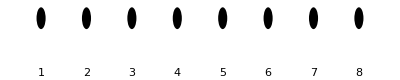

```mathematica
(* Picture of the chain sites *)
Chain[s_]:=Graphics[Table[{Disk[{i,0},0.1],Text[i,{i,-0.5}]},{i,1,s}]]
Chain[8]
```

```mathematica
(* Pictures of the chains in the DMRG procedure *)
DMRGChainLR[s_]:=Graphics[{Yellow,Rectangle[{0.5,-0.3},{s+0.5,0.3}],LightBlue,Rectangle[{s+0.5,-0.3},{2*s+0.5,0.3}],Table[{Red,Disk[{i,0},0.1],Black,Text[i,{i,-0.5}]},{i,1,s}],Black,Table[{Blue,Disk[{i,0},0.1],Black,Text[i,{i,-0.5}]},{i,s+1,2*s}],Black,Black,Text["Left Block",{s/2+0.5,0.4}],Text["Right Block",{s+s/2+0.5,0.4}]}]
DMRGChainAddition[s_]:=Graphics[{Yellow,Rectangle[{0.5,-0.3},{s+0.5,0.3}],LightBlue,Rectangle[{s+0.5,-0.3},{2*s+0.5,0.3}],Table[{Red,Disk[{i,0},0.1],Black,Text[i,{i,-0.5}]},{i,1,s}],Black,Circle[{s,0},0.3],Table[{Blue,Disk[{i,0},0.1],Black,Text[i,{i,-0.5}]},{i,s+1,2*s}],Black,Circle[{s+1,0},0.3],Black,Text["Left Block",{s/2+0.5,0.4}],Text["Right Block",{s+s/2+0.5,0.4}]}]
DMRGChainSB[s_]:=Graphics[{Orange,Opacity[0.4],Rectangle[{0.2,-0.8},{2*s+0.8,0.8}],Opacity[1],Yellow,Rectangle[{0.5,-0.3},{s+0.5,0.3}],LightBlue,Rectangle[{s+0.5,-0.3},{2*s+0.5,0.3}],Table[{Red,Disk[{i,0},0.1],Black,Text[i,{i,-0.5}]},{i,1,s}],Black,Table[{Blue,Disk[{i,0},0.1],Black,Text[i,{i,-0.5}]},{i,s+1,2*s}],Black,Black,Text["Left Block",{s/2+0.5,0.4}],Text["Right Block",{s+s/2+0.5,0.4}],Text["Super Block",{s+0.5,0.7}]}]
```

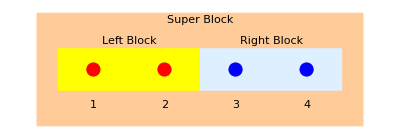

```mathematica
DMRGChainSB[2]
```

#### Exact theoretical results for the XY model spectrum (Lieb Schultz Mattis)

```mathematica
(*The ground state energy of the isotropic XY model with OBC*)
ϵ[k_,n_]:=-2 Cos[(π k)/(n+1)];
E0exact[n_]:=∑_(k=1)^Floor[n/2] ϵ[k,n]
E1exact[n_]:=∑_(k=1)^(Floor[n/2]-1) ϵ[k,n]
E1bexact[n_]:=∑_(k=1)^(Floor[n/2]+1) ϵ[k,n]
```

```mathematica
(* Exact values of the energy *)
E0exact[4]//N
E1exact[4]//N
E1bexact[4]//N
```

-2.23607

-1.61803

-1.61803

#### Density Matrix Renormalization Group (DMRG) approach step by step for better understanding of the process

```mathematica
(* Define σ^+, σ^- and I *)
sp={{0,1},{0,0}}; (* σ^+*)
sm={{0,0},{1,0}}; (* σ^-*)
id={{1,0},{0,1}};(* I *)
(* Define Id[m] as identity matrix m x m *)
Id[m_]:=IdentityMatrix[{m,m}];
Print["σ^+=",sp//MatrixForm,"  ","σ^-=",sm//MatrixForm,"  ","I=",id//MatrixForm,"  Id[3]=",Id[3]//MatrixForm]
```

σ^+=(0 | 1
0 | 0)  σ^-=(0 | 0
1 | 0)  I=(1 | 0
0 | 1)  Id[3]=(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

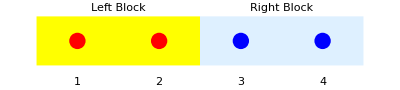

```mathematica
(* Step 1: Create Left and Right Blocks *)
(* Hamiltonian Left Block HL[2] = σ^+⊗ σ^- + σ^-⊗ σ^+ *)
HL[2]=KroneckerProduct[sp,sm]+KroneckerProduct[sm,sp];
(* Spin plus Left Block SpL[2] = I ⊗ σ^+ *)
SpL[2]=KroneckerProduct[id,sp];
(* Spin minus Left Block SmL[2] = I ⊗ σ^- *)
SmL[2]=KroneckerProduct[id,sm];
(* Hamiltonian Right Block HR[2] = σ^+⊗ σ^- + σ^-⊗ σ^+*)
HR[2]=KroneckerProduct[sp,sm]+KroneckerProduct[sm,sp];
(* Spin plus Right Block SpR[2] = σ^+ ⊗ I *)
SpR[2]=KroneckerProduct[sp,id];
(* Spin minus Right Block SmL[2] = σ^- ⊗ I *)
SmR[2]=KroneckerProduct[sm,id];
(* Graphic visualization: Picture of the spin chain  *)
DMRGChainLR[2]
```

```mathematica
(* Step 2: Create a Super Block Subscript[H, SB][4] = HL[2] ⊗ Id[2^2] + Id[2^2] ⊗ HR[2] + SpL[2] ⊗ SmR[2] + SmL[2] ⊗ SpR[2]  *)
(* This is equivalent to Subscript[H, SB][4] = (σ^+⊗ σ^- + σ^-⊗ σ^+) ⊗ I ⊗ I + I ⊗ I ⊗ (σ^+⊗ σ^- + σ^-⊗ σ^+)+ I ⊗ (σ^+⊗ σ^- + σ^-⊗ σ^+) ⊗ I *)
(* and corresponds to n = 4 XY chain *)
HSB[4]=KroneckerProduct[HL[2],Id[2^2]]+KroneckerProduct[Id[2^2],HR[2]]+KroneckerProduct[SpL[2],SmR[2]]+KroneckerProduct[SmL[2],SpR[2]];
(* Picture of the spin chain Super Block *)
DMRGChainSB[2]
```

-Graphics-

```mathematica
(* Step 3: Find the ground state energy and the wave function (we subtract identity matrix in order for the ground energy to be the energy with the biggest magnitude) *)
esys[4]=Eigensystem[HSB[4]-Id[2^4]//N,1];
(* the ground energy *)
E0[4]=esys[4][[1]]+1
(* the ground energy wave function *)
psi0[4]=esys[4][[2]]
```

{-2.23607}

{{0.,0.,0.,-0.223607,0.,0.5,-0.447214,0.,0.,-0.447214,0.5,0.,-0.223607,0.,0.,0.}}

```mathematica
(* Exact result for the ground energy of the n = 4 XY Hamiltonian*)
E0exact[4]//N
```

-2.23607

```mathematica
(* Step 4: Construct the left and right density matrices for the left and right blocks respectively *)
(* Reshape the ground state |ψ> = ∑_(a=1)^16 Subscript[ψ, a]|a> into LR form |ψ> = ∑_(i,j=1)^4 Subscript[ψ, ij] |i>_L ⊗ |j>_R *)
psiLR[4]=ArrayReshape[psi0[4],{2^2,2^2}];
(* Construct the left Density Matrtix Subscript[ρ, L] = ψ*ψ† *)
rhoL[2]=psiLR[4].psiLR[4]†;
(* Construct the right Density Matrtix Subscript[ρ, R] = (ψ†*ψ)^T *)
rhoR[2]=Transpose[psiLR[4]†.psiLR[4]];
```

```mathematica
(* Eigenvalues of the Left Density matrix *)
(* These are probabilities, thus they all must be positive and <= 1 *)
(* Their sum must be equal to 1 *)
SprhoL[2]=Eigenvalues[rhoL[2]]
```

{0.897214,0.05,0.05,0.0027864}

```mathematica
Total[SprhoL[2]]
```

1.

```mathematica
(* Matrix of the eigenvectors of the left Density matrix. Its columns are the eigenvectors *)
UL[2]=Transpose[Eigenvectors[rhoL[2]]];
(* Matrix of the eigenvectors of the right Density matrix. Its columns are the eigenvectors *)
UR[2]=Transpose[Eigenvectors[rhoR[2]]];
```

```mathematica
(* Step 5: Perform a change of basis *)
(* The left and right density matrices are diagonal in these bases *)
ConjugateTranspose[UL[2]].rhoL[2].UL[2]//Chop//MatrixForm
ConjugateTranspose[UR[2]].rhoR[2].UR[2]//Chop//MatrixForm
```

(0.897214 | 0 | 0 | 0
0 | 0.05 | 0 | 0
0 | 0 | 0.05 | 0
0 | 0 | 0 | 0.0027864)

(0.897214 | 0 | 0 | 0
0 | 0.05 | 0 | 0
0 | 0 | 0.05 | 0
0 | 0 | 0 | 0.0027864)

```mathematica
(* Left blocks in the new basis OverBar[HL] = UL†*HL*UL, OverBar[SpL] = UL†*SpL*UL, OverBar[SmL] = UL†*SmL*UL *)
HLb[2]=ConjugateTranspose[UL[2]].HL[2].UL[2];
SpLb[2]=ConjugateTranspose[UL[2]].SpL[2].UL[2];
SmLb[2]=ConjugateTranspose[UL[2]].SmL[2].UL[2];
(* Right blocks in the new basis OverBar[HR] = UR†*HR*UR, OverBar[SpR] = UR†*SpR*UR, OverBar[SmR] = UR†*SmR*UR*)
HRb[2]=ConjugateTranspose[UR[2]].HR[2].UR[2];
SpRb[2]=ConjugateTranspose[UR[2]].SpR[2].UR[2];
SmRb[2]=ConjugateTranspose[UR[2]].SmR[2].UR[2];
```

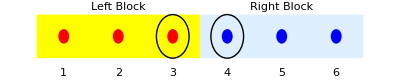

```mathematica
(* Step 1 again: Grow Left and Right blocks by one site *)
(* HL[3] = OverBar[HL][2] ⊗ I + OverBar[Sp] L[2] ⊗ σ^- + OverBar[SmL][2] ⊗ σ^+  *)
HL[3]=KroneckerProduct[HLb[2],id]+KroneckerProduct[SpLb[2],sm]+KroneckerProduct[SmLb[2],sp];
(* SpL[3] = I ⊗ I ⊗ σ^+ *)
SpL[3]=KroneckerProduct[Id[2^2],sp];
(* SmL[3] = I ⊗ I ⊗ σ^- *)
SmL[3]=KroneckerProduct[Id[2^2],sm];
(* HR[3] =I ⊗ OverBar[HR][2] + σ^- ⊗ OverBar[Sp]R[2] + σ^+ ⊗ OverBar[SmR][2] *)
HR[3]=KroneckerProduct[id,HRb[2]]+KroneckerProduct[sm,SpRb[2]]+KroneckerProduct[sp,SmRb[2]];
(* SpR[3] =  σ^+ ⊗ I ⊗ I *)
SpR[3]=KroneckerProduct[sp,Id[2^2]];
(* SmR[3] =  σ^- ⊗ I ⊗ I *)
SmR[3]=KroneckerProduct[sm,Id[2^2]];
(* Picture of the spin chain with added new sites *)
DMRGChainAddition[3]
```

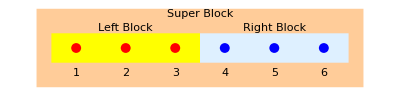

```mathematica
(* Step  2 again: Create a Super Block Subscript[H, SB][6]= HL[3] ⊗ I ⊗ I ⊗ I + I ⊗ I ⊗ I ⊗ HR[3] + SpL[3] ⊗ SmR[3] + SmL[3] ⊗ SpR[3]  *)
(* It corresponds to n = 6 XY chain *)
HSB[6]=KroneckerProduct[HL[3],Id[2^3]]+KroneckerProduct[Id[2^3],HR[3]]+KroneckerProduct[SpL[3],SmR[3]]+KroneckerProduct[SmL[3],SpR[3]];
(* Picture of the spin chain Super Block *)
DMRGChainSB[3]
```

```mathematica
(* Step 3again : Find the ground state energy and the wave function(we subtract identity matrix in order for the ground energy to be the energy with the biggest magnitude) *)
esys[6]=Eigensystem[HSB[6]-Id[2^6]//N,1];
E0[6]=esys[6][[1]]+1
psi0[6]=esys[6][[2]];
```

{-3.49396}

```mathematica
(* Exact result for the ground energy of the n = 6 XY Hamiltonian*)
E0exact[6]//N
```

-3.49396

```mathematica
(* Step 4 again: Construct left and right density matrices for the left and right blocks respectively *)
(* Reshape the ground state |ψ> = ∑_(a=1)^64 Subscript[ψ, a]|a> into LR form |ψ> = ∑_(i,j=1)^8 Subscript[ψ, ij] |i>_L ⊗ |j>_R *)
psiLR[6]=ArrayReshape[psi0[6],{2^3,2^3}];
(* Construct the left Density Matrtix Subscript[ρ, L] = ψ*ψ† *)
rhoL[3]=psiLR[6].psiLR[6]†;
(* Construct the right Density Matrtix Subscript[ρ, R] = (ψ†*ψ)^T *)
rhoR[3]=Transpose[psiLR[6]†.psiLR[6]];
```

```mathematica
(* Matrix of the eigenvectors of the left Density matrix. Its columns are the eigenvectors *)
UL[3]=Transpose[Eigenvectors[rhoL[3]//N]];
(* Matrix of the eigenvectors of the right Density matrix. Its columns are the eigenvectors *)
UR[3]=Transpose[Eigenvectors[rhoR[3]//N]];
```

```mathematica
(* Step 5 again: Perform a change of basis with truncation *)
(* The number of highest probability states we keep *)
m=6;
```

```mathematica
(* Density matrix Subscript[ρ, L] in the new truncated basis OverBar[Subscript[ρ, L]] = UL†*Subscript[ρ, L]*UL*)
rhoLb[3]=UL[3][[;;,1;;Min[m,2^3]]]†.rhoL[3].UL[3][[;;,1;;Min[m,2^3]]]//Chop;
rhoLb[3]//MatrixForm
```

(0.498138 | 0 | 0 | 0 | 0 | 0
0 | 0.498138 | 0 | 0 | 0 | 0
0 | 0 | 0.000930269 | 0 | 0 | 0
0 | 0 | 0 | 0.000930269 | 0 | 0
0 | 0 | 0 | 0 | 0.000930269 | 0
0 | 0 | 0 | 0 | 0 | 0.000930269)

```mathematica
(* Truncation Error *)
TruncationErrorL[3]=1-Tr[rhoLb[3]]
```

3.47455×10^-6

```mathematica
(* Truncated Left blocks in the new basis OverBar[HL] = UL†*HL*UL, OverBar[SpL] = UL†*SpL*UL, OverBar[SmL] = UL†*SmL*UL *)
HLb[3]=UL[3][[;;,1;;Min[m,2^3]]]†.HL[3].UL[3][[;;,1;;Min[m,2^3]]];
SpLb[3]=UL[3][[;;,1;;Min[m,2^3]]]†.SpL[3].UL[3][[;;,1;;Min[m,2^3]]];
SmLb[3]=UL[3][[;;,1;;Min[m,2^3]]]†.SmL[3].UL[3][[;;,1;;Min[m,2^3]]];
(* Truncated Right blocks in the new basis OverBar[HR] = UR†*HR*UR, OverBar[SpR] = UR†*SpR*UR, OverBar[SmR] = UR†*SmR*UR *)
HRb[3]=UR[3][[;;,1;;Min[m,2^3]]]†.HR[3].UR[3][[;;,1;;Min[m,2^3]]];
SpRb[3]=UR[3][[;;,1;;Min[m,2^3]]]†.SpR[3].UR[3][[;;,1;;Min[m,2^3]]];
SmRb[3]=UR[3][[;;,1;;Min[m,2^3]]]†.SmR[3].UR[3][[;;,1;;Min[m,2^3]]];
```

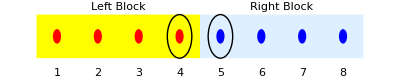

```mathematica
(* Step 1 again again: Grow Left and Right blocks by one site *)
(* HL[4] = OverBar[HL][3] ⊗ I + OverBar[Sp] L[3] ⊗ σ^- + OverBar[SmL][3] ⊗ σ^+  *)
HL[4]=KroneckerProduct[HLb[3],id]+KroneckerProduct[SpLb[3],sm]+KroneckerProduct[SmLb[3],sp];
(* SpL[4] = Subscript[I, mxm] ⊗ σ^+ *)
SpL[4]=KroneckerProduct[Id[m],sp];
(* SmL[4] = Subscript[I, mxm] ⊗ σ^- *)
SmL[4]=KroneckerProduct[Id[m],sm];
(* HR[4] =Subscript[I, mxm] ⊗ OverBar[HR][3] + σ^- ⊗ OverBar[Sp]R[3] + σ^+ ⊗ OverBar[SmR][3] *)
HR[4]=KroneckerProduct[id,HRb[3]]+KroneckerProduct[sm,SpRb[3]]+KroneckerProduct[sp,SmRb[3]];
(* SpR[4] =  σ^+ ⊗ Subscript[I, mxm] *)
SpR[4]=KroneckerProduct[sp,Id[m]];
(* SmR[4] =  σ^- ⊗ Subscript[I, mxm] *)
SmR[4]=KroneckerProduct[sm,Id[m]];
(* Picture of the spin chain with added new sites *)
DMRGChainAddition[4]
```

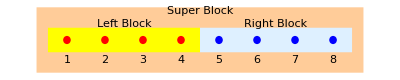

```mathematica
(* Step 2 again agaub : Create a Super Block Subscript[H, SB][8]= HL[4] ⊗ Subscript[I, 2mx2m] + Subscript[I, 2mx2m] ⊗ HR[4] + SpL[4] ⊗ SmR[4] + SmL[4] ⊗ SpR[4]  *)
(* It corresponds to n = 8 XY chain *)
HSB[8]=KroneckerProduct[HL[4],Id[2m]]+KroneckerProduct[Id[2m],HR[4]]+KroneckerProduct[SpL[4],SmR[4]]+KroneckerProduct[SmL[4],SpR[4]];
(* Picture of the spin chain Super Block *)
DMRGChainSB[4]
```

```mathematica
(* Step 3 again again : Find the ground state energy and the wave function (we subtract identity matrix in order for the ground energy to be the energy with the biggest magnitude) *)
esys[8]=Eigensystem[HSB[8]-Id[(2*m)^2]//N,1];
E0[8]=esys[8][[1]]+1
psi0[8]=esys[8][[2]];
```

{-4.75869}

```mathematica
(* Exact result for the ground energy of the n = 8 XY Hamiltonian*)
E0exact[8]//N
```

-4.75877

```mathematica
AbsoluteError=E0[8]-E0exact[8]//N
RelativeError=AbsoluteError/(-E0exact[8])//N
```

{0.00008347}

{0.0000175403}

#### Density Matrix Renormalization Group (DMRG) approach using a loop

```mathematica
(* Define σ^+, σ^- and I *)
sp={{0,1},{0,0}}; (* σ^+*)
sm={{0,0},{1,0}}; (* σ^-*)
id={{1,0},{0,1}};(* I *)
Print["σ^+=",sp//MatrixForm,"  ","σ^-=",sm//MatrixForm,"  ","I=",id//MatrixForm]
(* Define  Id[m] as identity matrix m x m *)
Id[m_]:=IdentityMatrix[{m,m}];
```

σ^+=(0 | 1
0 | 0)  σ^-=(0 | 0
1 | 0)  I=(1 | 0
0 | 1)

```mathematica
(*number of states we keep after truncation *)
m=10;
```

```mathematica
(* Create Initial Left and Right blocks *)
(* Hamiltonian Block Left HL[2] = σ^+⊗ σ^- + σ^-⊗ σ^+ *)
HLb[2]=KroneckerProduct[sp,sm]+KroneckerProduct[sm,sp]//N;
(* Spin plus Block Left SpL[2] = I ⊗ σ^+ *)
SpLb[2]=KroneckerProduct[id,sp]//N;
(* Spin minus Block Left SmL[2] = I ⊗ σ^- *)
SmLb[2]=KroneckerProduct[id,sm]//N;
(* Hamiltonian Block Right HR[2] = σ^+⊗ σ^- + σ^-⊗ σ^+*)
HRb[2]=KroneckerProduct[sp,sm]+KroneckerProduct[sm,sp]//N;
(* Spin plus Block Right SpR[2] = σ^+ ⊗ I *)
SpRb[2]=KroneckerProduct[sp,id]//N;
(* Spin minus Block Right SmL[2] = σ^- ⊗ I *)
SmRb[2]=KroneckerProduct[sm,id]//N;
(* Graphic visualization *)
DMRGChainLR[2]
```

-Graphics-

-----------------------------------------------

Iteration: 1

Grow Left and Right blocks by one site:

-Graphics-

Form a Super Block:

-Graphics-

Ground energy of the XY chain of 6 sites E0 = -3.49396

Absolute error: |E0 - E0_exact| = 2.44249×10^-15

Relative error: |E0/E0_exact - 1| = 7.77156×10^-16

Truncation Error Left = -2.22045×10^-16

Truncation Error Right = -2.22045×10^-16

-----------------------------------------------

Iteration: 2

Grow Left and Right blocks by one site:

-Graphics-

Form a Super Block:

-Graphics-

Ground energy of the XY chain of 8 sites E0 = -4.75877

Absolute error: |E0 - E0_exact| = 8.32667×10^-16

Relative error: |E0/E0_exact - 1| = 2.22045×10^-16

Truncation Error Left = 5.71973×10^-7

Truncation Error Right = 5.71973×10^-7

-----------------------------------------------

Iteration: 3

Grow Left and Right blocks by one site:

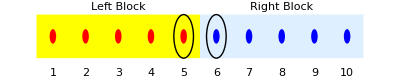

Form a Super Block:

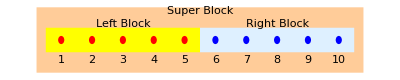

Ground energy of the XY chain of 10 sites E0 = -6.02666

Absolute error: |E0 - E0_exact| = 0.0000173089

Relative error: |E0/E0_exact - 1| = 2.87204×10^-6

Truncation Error Left = 7.16587×10^-7

Truncation Error Right = 7.16587×10^-7

-----------------------------------------------

Iteration: 4

Grow Left and Right blocks by one site:

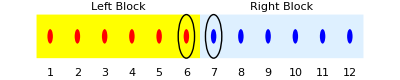

Form a Super Block:

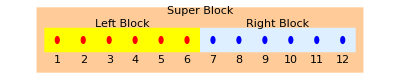

Ground energy of the XY chain of 12 sites E0 = -7.29619

Absolute error: |E0 - E0_exact| = 0.000044737

Relative error: |E0/E0_exact - 1| = 6.13152×10^-6

Truncation Error Left = 3.78817×10^-6

Truncation Error Right = 3.78817×10^-6

-----------------------------------------------

Iteration: 5

Grow Left and Right blocks by one site:

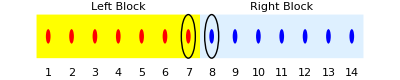

Form a Super Block:

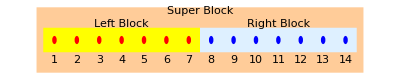

Ground energy of the XY chain of 14 sites E0 = -8.56664

Absolute error: |E0 - E0_exact| = 0.000130983

Relative error: |E0/E0_exact - 1| = 0.0000152897

Truncation Error Left = 4.35009×10^-6

Truncation Error Right = 4.35009×10^-6

-----------------------------------------------

Iteration: 6

Grow Left and Right blocks by one site:

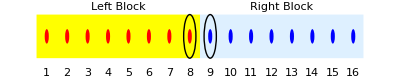

Form a Super Block:

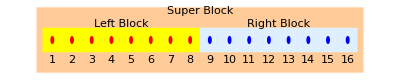

Ground energy of the XY chain of 16 sites E0 = -9.83773

Absolute error: |E0 - E0_exact| = 0.00022375

Relative error: |E0/E0_exact - 1| = 0.0000227435

Truncation Error Left = 9.75085×10^-6

Truncation Error Right = 9.75085×10^-6

-----------------------------------------------

Iteration: 7

Grow Left and Right blocks by one site:

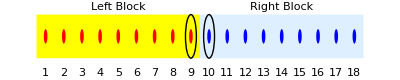

Form a Super Block:

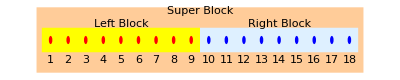

Ground energy of the XY chain of 18 sites E0 = -11.1092

Absolute error: |E0 - E0_exact| = 0.000409395

Relative error: |E0/E0_exact - 1| = 0.0000368507

Truncation Error Left = 0.0000101453

Truncation Error Right = 0.0000101453

-----------------------------------------------

Iteration: 8

Grow Left and Right blocks by one site:

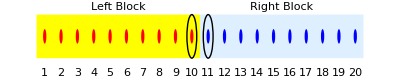

Form a Super Block:

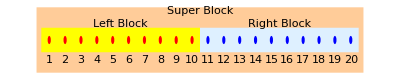

Ground energy of the XY chain of 20 sites E0 = -12.3809

Absolute error: |E0 - E0_exact| = 0.000584261

Relative error: |E0/E0_exact - 1| = 0.0000471883

Truncation Error Left = 0.0000171084

Truncation Error Right = 0.0000171084

```mathematica
(* Start DMRG interations *)
For[s=3,s<=10,s++,
Print["-----------------------------------------------" ];
Print["Iteration: " , s-2];
(* Step 1: Grow Left and Right blocks by one site *)
Print["Grow Left and Right blocks by one site:"];
(* HL[s] = OverBar[HL][s-1] ⊗ I + OverBar[Sp] L[s-1] ⊗ σ^- + OverBar[SmL][s-1] ⊗ σ^+  *)
HL[s]=KroneckerProduct[HLb[s-1],id]+KroneckerProduct[SpLb[s-1],sm]+KroneckerProduct[SmLb[s-1],sp];
(* SpL[s] = Subscript[I, mxm] ⊗ σ^+ *)
SpL[s]=KroneckerProduct[Id[Min[m,2^(s-1)]],sp];
(* SmL[s] = Subscript[I, mxm] ⊗ σ^- *)
SmL[s]=KroneckerProduct[Id[Min[m,2^(s-1)]],sm];
(* HR[s] =I ⊗ OverBar[HR][s-1] + σ^- ⊗ OverBar[Sp]R[s-1] + σ^+ ⊗ OverBar[SmR][s-1] *)
HR[s]=KroneckerProduct[id,HRb[s-1]]+KroneckerProduct[sm,SpRb[s-1]]+KroneckerProduct[sp,SmRb[s-1]];
(* SpR[s] =  σ^+ ⊗ Subscript[I, mxm] *)
SpR[s]=KroneckerProduct[sp,Id[Min[m,2^(s-1)]]];
(* SmR[s] =  σ^- ⊗ Subscript[I, mxm] *)
SmR[s]=KroneckerProduct[sm,Id[Min[m,2^(s-1)]]];
(* Graphic visualization *)
Print[DMRGChainAddition[s]];
(* Step 2: Create a Super Block Subscript[H, SB][2s]= HL[s] ⊗ Subscript[I, 2mx2m] +  Subscript[I, 2mx2m]  ⊗ HR[s] + SpL[s] ⊗ SmR[s] + SmL[s] ⊗ SpR[s]  *)
(* It corresponds to n = 2s XY chain *)
HSB[2s]=KroneckerProduct[HL[s],Id[Min[2m,2^s]]]+KroneckerProduct[Id[Min[2m,2^s]],HR[s]]+KroneckerProduct[SpL[s],SmR[s]]+KroneckerProduct[SmL[s],SpR[s]];
Print["Form a Super Block:"];
Print[DMRGChainSB[s]];
(* Step 3: Find the ground state energy and the wave function (we subtract identity matrix in order for the ground energy to be the energy with the biggest magnitude) *)
esys[2s]=Eigensystem[HSB[2s]-Id[Min[2m,2^s]^2],1,Method->{"Arnoldi","Criteria"->"Magnitude"}];
E0[2*s]=esys[2*s][[1]]+1;
Print["Ground energy of the XY chain of ", 2*s," sites E0 = ",E0[2s][[1]] ];
Print["Absolute error: |E0 - E0_exact| = ", Abs[E0[2s][[1]]  - E0exact[2s] ]];
Print["Relative error: |E0/E0_exact - 1| = ", Abs[E0[2s][[1]]/E0exact[2s]-1]];
psi0[2s]=esys[2*s][[2]];
(* Step 4: Construct left and right density matrices for the left and right blocks respectively *)
(* Reshape the ground state |ψ> = ∑_(a=1)^((2m)^2) Subscript[ψ, a]|a> into LR form |ψ> = ∑_(i,j=1)^(2m) Subscript[ψ, ij] |i>_L ⊗ |j>_R *)
psiLR[2*s]=ArrayReshape[psi0[2*s],{Min[2m,2^s],Min[2m,2^s]}];
(* Construct the left Density Matrtix Subscript[ρ, L] = ψ*ψ† *)
rhoL[s]=psiLR[2*s].psiLR[2*s]†;
(* Construct the right Density Matrtix Subscript[ρ, R] = (ψ†*ψ)^T *)
rhoR[s]=Transpose[psiLR[2*s]†.psiLR[2*s]];
(* Matrix of the eigenvectors of the left Density matrix. Its columns are the eigenvectors *)
UL[s]=Transpose[Eigenvectors[rhoL[s]]];
(* Matrix of the eigenvectors of the right Density matrix. Its columns are the eigenvectors *)
UR[s]=Transpose[Eigenvectors[rhoR[s]]];
(* Step 5: Perform a change of basis with truncation *)
(* Truncation Errors *)
(* Density matrix Subscript[ρ, L] in the new truncated basis OverBar[Subscript[ρ, L]] = UL†*Subscript[ρ, L]*UL*)
rhoLb[s]=UL[s][[;;,1;;Min[m,2^s]]]†.rhoL[s].UL[s][[;;,1;;Min[m,2^s]]];
(* Density matrix Subscript[ρ, L] in the new truncated basis OverBar[Subscript[ρ, R]] = UR†*Subscript[ρ, R]*UR*)
rhoRb[s]=UR[s][[;;,1;;Min[m,2^s]]]†.rhoR[s].UR[s][[;;,1;;Min[m,2^s]]];
TruncationErrorL[s]=1-Tr[rhoLb[s]];
TruncationErrorR[s]=1-Tr[rhoRb[s]];
Print["Truncation Error Left = ",TruncationErrorL[s]];
Print["Truncation Error Right = ",TruncationErrorR[s]];
(* Truncated Left blocks in the new basis OverBar[HL] = UL†*HL*UL, OverBar[SpL] = UL†*SpL*UL, OverBar[SmL] = UL†*SmL*UL *)
HLb[s]=UL[s][[;;,1;;Min[m,2^s]]]†.HL[s].UL[s][[;;,1;;Min[m,2^s]]];
SpLb[s]=UL[s][[;;,1;;Min[m,2^s]]]†.SpL[s].UL[s][[;;,1;;Min[m,2^s]]];
SmLb[s]=UL[s][[;;,1;;Min[m,2^s]]]†.SmL[s].UL[s][[;;,1;;Min[m,2^s]]];
(* Truncated Right blocks in the new basis OverBar[HR] = UR†*HR*UR, OverBar[SpR] = UR†*SpR*UR, OverBar[SmR] = UR†*SmR*UR  *)
HRb[s]=UR[s][[;;,1;;Min[m,2^s]]]†.HR[s].UR[s][[;;,1;;Min[m,2^s]]];
SpRb[s]=UR[s][[;;,1;;Min[m,2^s]]]†.SpR[s].UR[s][[;;,1;;Min[m,2^s]]];
SmRb[s]=UR[s][[;;,1;;Min[m,2^s]]]†.SmR[s].UR[s][[;;,1;;Min[m,2^s]]];]
```

```mathematica
(* Table of the exact ground state energies for the XY model *)
Table[E0exact[2*i]//N,{i,3,20}]
```

{-3.49396,-4.75877,-6.02667,-7.29623,-8.56677,-9.83795,-11.1096,-12.3815,-13.6536,-14.926,-16.1984,-17.471,-18.7437,-20.0164,-21.2892,-22.562,-23.8349,-25.1078}